```mathematica
If[StringTake[$SystemID,3]=="Win",
SetDirectory["C:\\Users\\pwrzo\\Documents\\GitHub\\AvoidedQP\\implementation\\"],
SetDirectory["~/Documents/GitHub/AvoidedQP/reimplementation/"]
]
```

/Users/pwrzosek/Documents/GitHub/AvoidedQP/reimplementation

```mathematica
AppendTo[$Path,"~/MathematicaPkg/"];
<<CustomTicks`;
<<MaTeX`;
```

```mathematica
getAssoc[head_,JRange_,tail_]:=(
result={};
Do[(
file=StringJoin[head,"_1.0_",J,"_",tail,".json"];
niData=Import[StringJoin["data/", file],"RawJSON"];
result=Join[result,qpData];
),{J,JRange}];
result
)
```

```mathematica
getStruct[ds_]:=(
sizeAvail=Normal[DeleteDuplicates[ds[Take,"size"]]];
anisotropyAvail=Normal[DeleteDuplicates[ds[Take,"anisotropy"]]];
couplingAvail=Normal[DeleteDuplicates[ds[Take,"coupling"]]];
hoppingAvail=Normal[DeleteDuplicates[ds[Take,"hopping"]]];
<|"size"->sizeAvail,"anisotropy"->anisotropyAvail,"coupling" ->couplingAvail, "hopping"->hoppingAvail|>
)
```

```mathematica
extractData[ds_,directive_,keys_]:=(
data=Apply[ds,directive];
x=(data[Take,keys[[1]]]//Normal);
y=(data[Take,keys[[2]]]//Normal);
y=y[[;;,1]];

Do[(
x=Table[x[[i]],{i,2,Length[x]-1}];
y=Table[(y[[i+1]]-y[[i-1]])/0.2,{i,2,Length[y]-1}];
),{it,0}];

result=Table[{x[[it]],y[[it]]},{it,Length[x]}];
Clear[x,y];
result
)
```

```mathematica
StandardNumberForm[x_]:=If[FractionalPart[x]==0,IntegerPart[x],x];
tlf=(MaTeX[ToString[StandardNumberForm[#]]]&);
```

```mathematica
getPlot[data_]:=(
SetOptions[LinTicks,TickLengthScale->2.5];
SetOptions[MaTeX,Magnification->1.8];

colors={Black};
pltStyle=Table[Directive[Dashed,color,Opacity[0.7]],{color,colors}];

fs=22;
plt=ListPlot[data,
PlotRange->{{0,4.0001},All},
ImageSize->360,
Frame->True,Axes->False,
FrameStyle->Directive[Black,fs,FontFamily->"CMU Serif"],
PlotMarkers->{"●", 12},

FrameLabel->{MaTeX["\\alpha"],MaTeX["\\mathrm{a.k.a.}~n_i"]},
LabelStyle->Directive[Black,12],
PlotStyle->pltStyle,
AspectRatio->.75,
FrameTicks->{{LinTicks[-2,2,0.5,5,TickLabelFunction->tlf],StripTickLabels[LinTicks[-2,2,0.5,5]]},{LinTicks[0,4.0,1,10,TickLabelFunction->tlf],StripTickLabels[LinTicks[0,4.0,1, 10]]}}
];

line1=Plot[{-0.0432x+793/2048},{x,0,1}];
line2=Plot[{(-0.0432+793/2048)/((2x+3)/5+(x-1)^2)},{x,1,4}];

Show[{plt},PlotRangeClipping->False]
)
```

```mathematica
makePlotsNi[]:=(
directive={Select[#coupling==J&]};
keys={"anisotropy","coefficients"};

plots={};
Do[(
a={};
AppendTo[a,extractData[niDataset,directive,keys]];
AppendTo[plots,getPlot[a]];
),{J,niAvail["coupling"]//Normal}];

plots
)
```

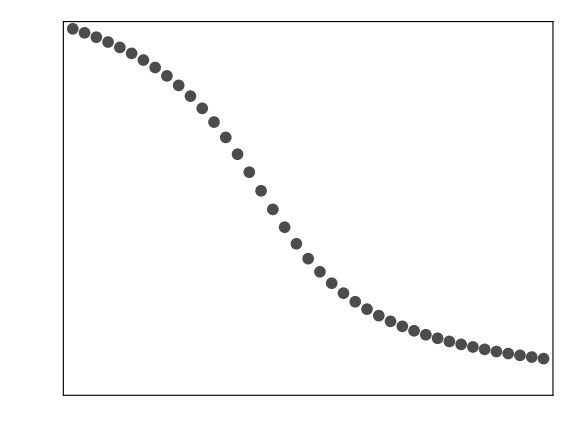

```mathematica
JRange={"0.4"};
tails={"24-2-24_0.0-0.1-4.0"};
niPlots={};
Do[(
niDataset=Dataset[getAssoc["ni",JRange,tail]];
niAvail=Dataset[getStruct[niDataset]];
AppendTo[niPlots,{Show[makePlotsNi[],ImageSize->Large]}];
),{tail,tails}]
Print[Grid[niPlots//Transpose]];
```

```mathematica
Export["ni.png",niPlots[[1,1]],ImageResolution->300]
```

ni.png